## Parameters

```mathematica
wd=NotebookDirectory[];
SetDirectory[wd];

(*Read parameter file into conf*)
ReadConf[filename_]:=Module[{res={},i,rawF,Ln,chk},
rawF=Import[filename];
For[i=1,i<=Length[rawF],++i,
If[rawF[[i]]=={},Continue[]];
If[StringTake[rawF[[i]],1][[1]]=="#",Continue[]];
Ln=StringSplit[rawF[[i]]][[1]];
If[NumericQ[ToExpression[Ln[[2]]]],AppendTo[res,Ln[[1]]->ToExpression[Ln[[2]]]],AppendTo[res,Ln[[1]]->Ln[[2]]]];
];
Association[res]
];
(*Parameters can be called same as in py*)
conf=ReadConf["../params"];
StateList={"1S","2S"};
```

### Matrix Elements

```mathematica
η[prel_,st_]:=conf["alphaS"]*conf["M"<>st]/(4*conf["NC"]*prel)
aB[st_]:=2/(conf["alphaS"]*conf["CF"]*conf["M"<>st]);
(*Matrix Elements*)
MOvLp[prel_,st_]:=Piecewise[{{
(((2^9)(Pi^2)(η[prel,st])(aB[st]^7)(prel^2)(1+η[prel,st]^2)(2+η[prel,st]*aB[st]*prel)^2)/((1+(aB[st]^2)(prel^2))^6(Exp[2Pi*η[prel,st]]-1)))*Exp[4η[prel,st]*ArcTan[aB[st]*prel]],st=="1S"},
{
(((2^18)(Pi^2)(η[prel,st])(aB[st]^7)(prel^2)(1+η[prel,st]^2))/((1+4(aB[st]^2)(prel^2))^6(Exp[2Pi*η[prel,st]]-1)))*Exp[4η[prel,st]*ArcTan[2aB[st]*prel]],st=="2S"}}];
```

## Dissociation Channels

### Real Gluon Absorption

```mathematica
(*Sampling integrand*)
Ig[q_,st_]:=Piecewise[{{(q^3)*Sqrt[conf["M"<>st](q-conf["E"<>st])](1/(Exp[q/conf["T"]]-1))MOvLp[Sqrt[conf["M"<>st](q-conf["E"<>st])],st],q>conf["E"<>st]},{0,q<=conf["E"<>st]}}];
(*IgMaxs=Table[Maximize[{Ig[q,StateList[[i]]],conf["E"<>StateList[[i]]]<q<20*conf["E"<>StateList[[i]]]},q][[1]],{i,1,Length[StateList]}];*)
Igs=Table[Ig[q,StateList[[i]]],{i,1,Length[StateList]}];
```

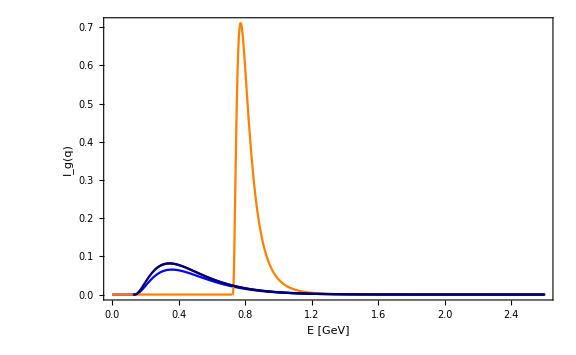

```mathematica
RGAIntPlot=Plot[Igs,{q,0,20*conf["E1S"]},PlotRange->All,PlotStyle->{Directive[Blue],Directive[Orange]},Frame->True,FrameLabel->{{"I_g(q)",""},{"E [GeV]","RGA Integrand"}},ImageSize->Large];
IgDat=Table[Transpose[{Range[conf["E1S"],20*conf["E"<>StateList[[i]]],(19*conf["E"<>StateList[[i]]])/(conf["NPts"]-1)],Flatten[Import["../export/rateRGA_"<>StateList[[i]]<>".tsv"]]}],{i,1,1}];
expRGAIntPlot=ListPlot[PyDat,PlotStyle->{Directive[{PointSize->0.003,Darker[Darker[Blue]]}],Directive[{PointSize->0.001,Darker[Orange]}]},Frame->True,FrameLabel->{{"I_g(q)",""},{"E [GeV]","RGA Integrand"}},ImageSize->Large];
Show[RGAIntPlot,expRGAIntPlot]
```

## Regeneration Channels

### Real Gluon Radiation